```mathematica
w1[ξ_]:=Piecewise[{{1-Abs[ξ],-1<ξ≤1}}]
w3[ξ_]:=Piecewise[{{-1/3 Abs[ξ]+1/2 Abs[ξ]^2-1/6 Abs[ξ]^3,-1<ξ≤1}}]
```

```mathematica
len[xs_]:=Length[xs]-1
enum[xs_]:=MapIndexed[{#2[[1]]-1,#1}&,xs]
```

```mathematica
lis[xs_,x_]:=Sum[xi[[2]]*w1[x len[xs]-xi[[1]]],{xi,enum[xs]}]
```

```mathematica
cis[xs_,xpps_,x_]:=lis[xs,x]+Sum[1/len[xpps]^2 xppi[[2]]*w3[x len[xpps]-xppi[[1]]],{xppi,enum[xpps]}]
```

```mathematica
c[k_,kdx_]:=-3 k^2 Sinc[kdx/2]^2(2+Cos[kdx])^-1
```

```mathematica
cisFourier[nn_,k_,x_]:=(
xs:=Table[n/nn,{n,0,nn}];
f1[ξ_]:=Cos[k ξ];
ys1=Map[f1,xs];
ypps1=Map[Re[c[k,k/nn]*f1[#]]&,xs];
cis[ys1,ypps1,x]
)
```

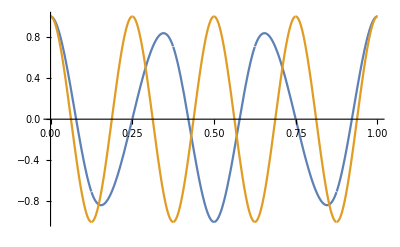

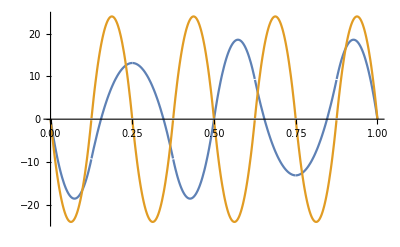

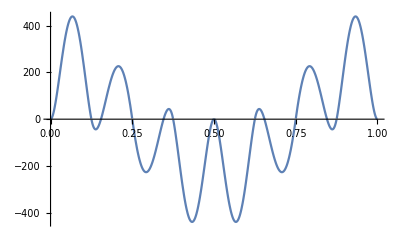

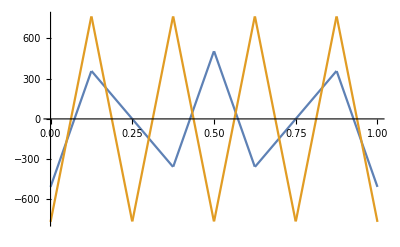

0

```mathematica
nn:=8;
λ1:=1/3;
k1:=(2π)/λ1;
λ2:=1/4;
k2:=(2π)/λ2;
fn1[x_]:=cisFourier[nn,k1,x]
fn2[x_]:=cisFourier[nn,k2,x]
Plot[{fn1[x],fn2[x]},{x,0,1}]

fnp1[x_]:=Evaluate[D[fn1[x],x]]
fnp2[x_]:=Evaluate[D[fn2[x],x]]
Plot[{fnp1[x],fnp2[x]},{x,0,1}]
Plot[{fnp1[x]*fnp2[x]},{x,0,1}]

fnpp1[x_]:=Evaluate[D[fnp1[x],x]]
fnpp2[x_]:=Evaluate[D[fnp2[x],x]]
Plot[{fnpp1[x],fnpp2[x]},{x,0,1}]

Integrate[fnp1[x]*fnp2[x],{x,0,1}]//Simplify
```

```mathematica
nn:=8;
Table[(
λ1:=1/n1;
k1:=(2π)/λ1;
λ2:=1/n2;
k2:=(2π)/λ2;
fn1[x_]:=cisFourier[nn,k1,x];
fn2[x_]:=cisFourier[nn,k2,x];
fnp1[x_]:=Evaluate[D[fn1[x],x]];
fnp2[x_]:=Evaluate[D[fn2[x],x]];

Integrate[fnp1[x]*fnp2[x],{x,0,1}]//Simplify
),{n1,1,nn/2},{n2,1,nn/2}]
```

{{-48/245 (-416+223 √2),0,0,0},{0,384/5,0,0},{0,0,48/245 (416+223 √2),0},{0,0,0,1536/5}}

```mathematica
{{-48/245 (-416+223 √2),0,0,0},{0,384/5,0,0},{0,0,48/245 (416+223 √2),0},{0,0,0,1536/5}}//MatrixForm//N
```

(19.7153 | 0. | 0. | 0.
0. | 76.8 | 0. | 0.
0. | 0. | 143.289 | 0.
0. | 0. | 0. | 307.2)

```mathematica
nn:=8;
Table[(
λ1:=1/n1;
k1:=(2π)/λ1;
λ2:=1/n2;
k2:=(2π)/λ2;
fn1[x_]:=cisFourier[nn,k1,x];
fn2[x_]:=cisFourier[nn,k2,x];

Integrate[fn1[x]*fn2[x],{x,0,1}]//Simplify
),{n1,1,nn/2},{n2,1,nn/2}]
```

{{(6112+523 √2)/13720,0,0,0},{0,17/35,0,0},{0,0,(6112-523 √2)/13720,0},{0,0,0,17/35}}

```mathematica
{{(6112+523 √2)/13720,0,0,0},{0,17/35,0,0},{0,0,(6112-523 √2)/13720,0},{0,0,0,17/35}}//N
```

{{0.49939,0.,0.,0.},{0.,0.485714,0.,0.},{0.,0.,0.391572,0.},{0.,0.,0.,0.485714}}

## Edge Centered

```mathematica
w1[ξ_]:=1-Abs[ξ]
w3[ξ_]:=-1/3 Abs[ξ]+1/2 Abs[ξ]^2-1/6 Abs[ξ]^3
```

```mathematica
w1[ξ_]:=1-ξ
w3[ξ_]:=-1/3 ξ+1/2 ξ^2-1/6 ξ^3
```

```mathematica
Δx:=l/nn
xn[n_]:=n Δx
```

```mathematica
c[k_]:=-k^2 Sinc[(k Δx)/2]^2 3/(2+Cos[k Δx])
```

```mathematica
func[x_,k_]:=(Exp[ⅈ k xn[n]]w1[(xn[n]-x)/Δx]+Δx^2 ck w3[(xn[n]-x)/Δx])
```

```mathematica
Simplify[D[func[x,k],x]]
```

(6 ⅇ^((ⅈ k l n)/nn) nn^2+ck (l^2 (2-6 n+3 n^2)-6 l (-1+n) nn x+3 nn^2 x^2))/(6 l nn)